# Homework 26

## Carter Colton

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica\360

## Problem 1 and 2

```mathematica
Import["C:\\Users\\carte\\OneDrive\\Documents\\Wolfram Mathematica\\360\\hw26problems.pdf"]
```

{-Graphics-,-Graphics-}

## Problem 3

### Part A

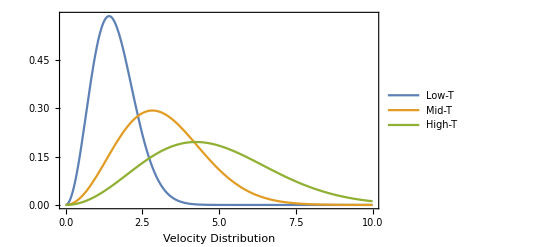

```mathematica
const=Sqrt[k*T/m];
const^-3;
const^-2;
const=1;
Pv1=4*Pi*v^2*(1/(2*Pi))^(3/2)*const^-3*Exp[-v^2/2*const^-2];
const=2;
Pv2=4*Pi*v^2*(1/(2*Pi))^(3/2)*const^-3*Exp[-v^2/2*const^-2];
const=3;
Pv3=4*Pi*v^2*(1/(2*Pi))^(3/2)*const^-3*Exp[-v^2/2*const^-2];
Plot[{Pv1,Pv2,Pv3},{v,0,10},Frame->True,FrameLabel->"Velocity Distribution",PlotLegends->{"Low-T","Mid-T","High-T"}]
```

### Part B

```mathematica
newconst=k*T/m;
eps=m*v^2/2;
Pv=4*Pi*v^2*(m/(2*Pi*k*T))^(3/2)*Exp[-m*v^2/(2*k*T)];
vmean=Sqrt[Simplify[Integrate[v^2*Pv,{v,0,Infinity}]]]
vmeansquared=vmean^2
vrms=Sqrt[vmeansquared]
x=Solve[D[Pv,v]==0,v];
vpeak=x[[3]]
```

ConditionalExpression[√3 √((k T)/m), Re[m/(k T)]>0]

ConditionalExpression[(3 k T)/m, Re[m/(k T)]>0]

ConditionalExpression[√3 √((k T)/m), Re[m/(k T)]>0]

{v→(√2 √k √T)/(√m)}

### Part C

```mathematica
m=(2.66*10^-23)/1000;
T=300;
k=1.38*10^-23;
vmean
vmeansquared
vrms
vpeak
```

683.313

466917.

683.313

{v→557.923}

## Problem 4

```mathematica
randomdir3D:=Module[{th,z,rho},th=RandomReal[{0,2 Pi}];
z=RandomReal[{-1,1}];
rho=Sqrt[1-z^2];
{rho Cos[th],rho Sin[th],z}]
collision3D[{vec1_,vec2_}]:=Module[{nvec,vnorm},nvec=randomdir3D;
vnorm=((vec2-vec1).nvec) nvec;
{vec1+vnorm,vec2-vnorm}]
maxbolt[{Nsize_,Nsteps_}] :=
Module[{papavec,new1,new2,ind1,ind2,velnorm,veldist,xdata,ydata},
papavec=Table[randomdir3D,Nsize];
Do[
ind1=RandomInteger[{1,Nsize}];
ind2=RandomInteger[{1,Nsize}];
{new1,new2}=collision3D[{papavec[[ind1]],papavec[[ind2]]}];
papavec[[ind1]]=new1;
papavec[[ind2]],
Nsteps];
velnorm=Norm/@papavec;
{xdata,ydata}=HistogramList[velnorm,50];
veldist={Drop[xdata,-1]+0.5*(xdata[[2]]-xdata[[1]]),ydata}//Transpose;
Return[{velnorm,veldist,Histogram[velnorm,50]}];
]
take1=maxbolt[{10000,10}];
take2=maxbolt[{10000,25}];
take3=maxbolt[{10000,50}];
take4=maxbolt[{10000,100}];
take5=maxbolt[{10000,75}];
take6=maxbolt[{10000,10^6}];
take6[[3]]
gooddata=take6[[2]];
partbfit=NonlinearModelFit[gooddata,a*x1^2*Exp[-b*x1^2],{a,b},x1]
A=1894.03;
B=-1.40623;
Show[Plot[A*v^2*Exp[B*v^2],{v,0,5}],ListPlot[gooddata]]
b=m/(2*k*T);
b=1.40623;
sqrtkToverm=(2*b)^(-1/2)
vrmsvpeakratiop=N[Sqrt[3/2]]
vpeaktrialrun=Solve[D[A*v^2*Exp[B*v^2],v]==0,v];
vpeak=vpeaktrialrun[[3]]
vpeak=0.84328;
vrms=Sqrt[3]*sqrtkToverm
vrmsvpeakratioreal=vrms/vpeak
```

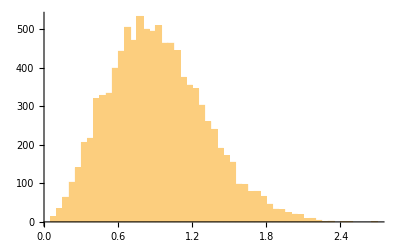

FittedModel[2063.83 ⅇ^(-1.4939 x1^2) x1^2]

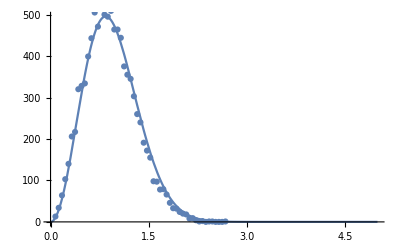

0.596289

1.22474

{v→0.84328}

1.0328

1.22474

```mathematica
(* 10^6 Nsteps *)
```